Box Spline functions, first a compact definition, then a verbose and easy to follow definition.
Evaluate ONE of the following cells before executing examples.

```mathematica
(*Box Spline Evaluation function, minimally coded for concise analytic solutions.
Assumes that Subscript[A, s]=Identity[s] (In n-dimensional space, the first n column vectors of A represent the unit cube.)*)
(*The technically correct, more general condition for computing that base case prevents concise analytic Mathematica solutions and is:
If[RegionMember[Parallelepiped[ConstantArray[0,Dimensions[A][[1]]],Transpose[A]],x],Det[A]^-1,0]*)
inZeroOne[x_]:=0≤x<1;
BoxEval[x_,A_]:=(
If[SquareMatrixQ[A],
If[AllTrue[Transpose[x][[1]],inZeroOne],1,0],
∫_0^1 BoxEval[x-t[x]*A[[All,Dimensions[A][[2]];;Dimensions[A][[2]]]],A[[All,1;;Dimensions[A][[2]]-1]]]ⅆt[x]
])
```

```mathematica
(*Box Spline Evaluation function, verbosely coded for ease of understanding and demonstration of the computing process*)
inZeroOne[x_]:=0≤x<1;
BoxEval[x_,A_,show_:True]:=(
If[show,(
Print[""];
Print["A:     ",MatrixForm[A]];
Print["x:     ",MatrixForm[x]];
)];
ADim = Dimensions[A];
If[SquareMatrixQ[A],
Return[If[AllTrue[Transpose[x][[1]],inZeroOne],1,0]],
(AMin=A[[All,ADim[[2]];;ADim[[2]]]];
ARest=A[[All,1;;ADim[[2]]-1]];
If[show,(
Print["AMin:  ",MatrixForm[AMin]];
Print["ARest: ",MatrixForm[ARest]];
)];
Return[ ∫_0^1 BoxEval[x-t[x]*AMin,ARest,show]ⅆt[x] ];)
])
```

Example of Box Splines in 2 Dimensions.
For each example, “g[x]” is the analytic solution that the “BoxEval” function should arrive at, and “f[x]” is the function produced automatically by Mathematica with the “BoxEval” function.

If[0≤x≤1,1,0]

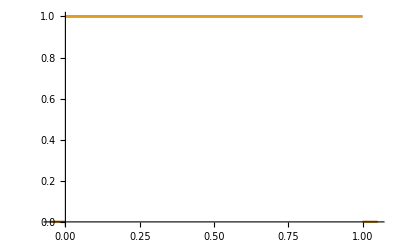

```mathematica
g[x_]=If[0≤x≤1,1,0]
(* f[x_]=BoxEval[(x),(1)] *)
Plot[{g[x],g[x]},{x,-.05,1.05}]
```

Piecewise[{{1, x==1}, {2-x, 1<x<2}, {x, 0<x<1}, {0, True}}]

Piecewise[{{2-x, 1≤x<2}, {x, 0<x<1}, {0, True}}]

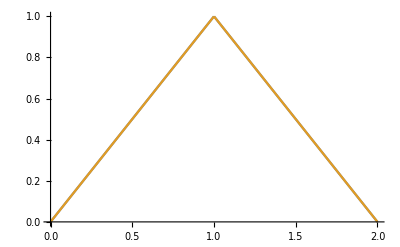

```mathematica
g[x_]=∫_0^1 If[0≤x-t≤1,1,0]ⅆt
f[x_]=BoxEval[(x),({{1, 1}})]
Plot[{f[x],g[x]},{x,0,2}]
```

Piecewise[{{x^2/2, 0<x≤1}, {1/2 (-3+6 x-2 x^2), 1<x<2}, {1/2 (9-6 x+x^2), 2≤x<3}, {0, True}}]

Piecewise[{{x^2/2, 0<x≤1}, {1/2 (-3+6 x-2 x^2), 1<x<2}, {1/2 (9-6 x+x^2), 2≤x<3}, {0, True}}]

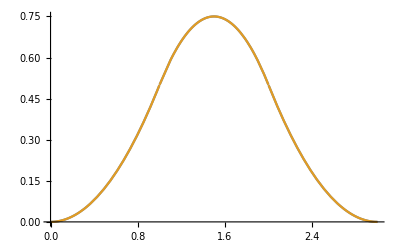

```mathematica
g[x_]=∫_0^1 ∫_0^1 If[0≤x-t-u≤1,1,0]ⅆuⅆt
f[x_]=BoxEval[(x),({{1, 1, 1}})]
Plot[{f[x],g[x]},{x,0,3}]
```

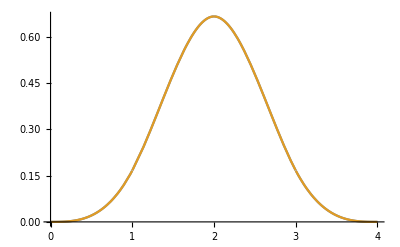

```mathematica
g[x_]=∫_0^1 ∫_0^1 ∫_0^1 If[0≤x-t-u-v≤1,1,0]ⅆvⅆuⅆt
f[x_]=BoxEval[(x),({{1, 1, 1, 1}})]
Plot[{f[x],g[x]},{x,0,4}]
```

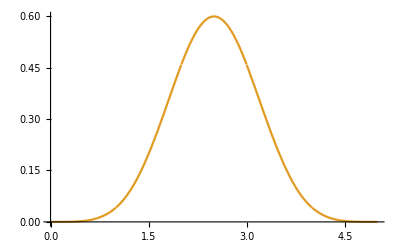

```mathematica
g[x_]=∫_0^1 ∫_0^1 ∫_0^1 ∫_0^1 If[0≤x-t-u-v-w≤1,1,0]ⅆwⅆvⅆuⅆt
f[x_]=BoxEval[(x),({{1, 1, 1, 1, 1}})]
Plot[{f[x],g[x]},{x,0,5}]
```

Examples of Box Splines in 3 Dimensions

```mathematica
f[x_,y_]=BoxEval[({{x}, {y}}),({{1, 0}, {0, 1}})]
Plot3D[f[x,y],{x,-0.05,1.05},{y,-0.05,1.05}]
```

If[0≤x<1&&0≤y<1,1,0]

-Graphics3D-

```mathematica
f[x_,y_]=BoxEval[({{x}, {y}}),({{1, 0, 1}, {0, 1, 0}})]
Plot3D[f[x,y],{x,0,2},{y,0,2}]
```

```mathematica
f[x_,y_]=BoxEval[({{x}, {y}}),({{1, 0, 0}, {0, 1, 1}})]
Plot3D[f[x,y],{x,0,2},{y,0,2}]
```

```mathematica
f[x_,y_]=BoxEval[({{x}, {y}}),({{1, 0, 1, 0}, {0, 1, 0, 1}})]
Plot3D[f[x,y],{x,0,2},{y,0,2}]
```

Piecewise[{{(-2+x) (-2+y), 1≤x<2&&1≤y<2}, {-x (-2+y), 0<x<1&&1≤y<2}, {-(-2+x) y, 1≤x<2&&0<y<1}, {x y, 0<x<1&&0<y<1}, {0, True}}]

-Graphics3D-

```mathematica
f[x_,y_]=BoxEval[({{x}, {y}}),({{1, 0, 1}, {0, 1, 1}})]
Plot3D[f[x,y],{x,0,2},{y,0,2}]
```

Piecewise[{{2-x, 1≤x<2&&y≥1&&x-y>0}, {x, 0<x<1&&x-y<0&&y≤1}, {2-y, 1≤x<2&&x-y≤0&&y<2}, {1+x-y, 0<x<1&&y>1&&x-y>-1}, {y, 0<x<1&&y>0&&x-y≥0}, {1-x+y, 1≤x<2&&x-y<1&&y<1}, {0, True}}]

-Graphics3D-

```mathematica
(*A [common] box spline studied by Powell and Sabin.*)
f[x_,y_]=BoxEval[({{x}, {y}}),({{1, 0, 1, 1}, {0, 1, 1, -1}})]
Plot3D[f[x,y],{x,0,3},{y,-1,2}]
```

(Piecewise[{{1/2 (2-x) (x-y)+1/8 (x-y)^2, 1<x≤2&&1<y<x}, {1/2+(2-x) (3-x)-1/2 (-2+x)^2, 5/2<x<3&&3-x<y≤-2+x}, {-1/2 (1-y)^2+1/8 (x-y)^2+(2-x) (-1+(x-y)/2+y), (1<x≤2&&2-x<y≤1)||(2<x≤5/2&&-2+x<y≤3-x)}, {1/2-1/2 (1-y)^2+(2-x) y, (2<x≤5/2&&0<y≤-2+x)||(5/2<x<3&&0<y≤3-x)}, {-1/2 (-2+x)^2+(2-x) (2-x+(x-y)/2)+1/8 (x-y)^2, (2<x≤5/2&&3-x<y<4-x)||(5/2<x<3&&-2+x<y<4-x)}, {0, True}}])+(Piecewise[{{1/4 (1+x-y)^2, 0<x≤1&&1<y<1+x}, {-2 (1/2-1/2 (-1+x)^2)+(2-x) (1+x-y), 3/2<x<2&&2-x<y≤-1+x}, {-2 (-1/2 (1-y)^2+1/8 (1+x-y)^2)+(1+x-y) (-1+1/2 (1+x-y)+y), (0<x≤1&&1-x<y≤1)||(1<x≤3/2&&-1+x<y≤2-x)}, {-2 (1/2-1/2 (1-y)^2)+(1+x-y) y, (1<x≤3/2&&0<y≤-1+x)||(3/2<x<2&&0<y≤2-x)}, {-2 (-1/2 (-1+x)^2+1/8 (1+x-y)^2)+(1-x+1/2 (1+x-y)) (1+x-y), (1<x≤3/2&&2-x<y<3-x)||(3/2<x<2&&-1+x<y<3-x)}, {0, True}}])+(Piecewise[{{-1/2+(1+1/2 (-2+y)) (2-y)+1/8 (2-y)^2, x==2&&0<y<1}, {-3/8 (2-y)^2+(2-y) (2+1/2 (-2+y)-y), x==2&&1≤y<2}, {-1/2+1/8 (x-y)^2+(2-y) (1+1/2 (-x+y)), 2<x<3&&-2+x<y≤1}, {-1/2 (-1+x)^2+(-1+x) (2-y), (1<x<3/2&&y==3-x)||(1<x<3/2&&x<y<3-x)}, {-1/2 (-1+x)^2+1/8 (x-y)^2+(2-y) (-1+x+1/2 (-x+y)), (1<x<3/2&&2-x<y≤x)||(3/2≤x<2&&2-x<y<3-x)}, {1/2 (2-y)^2, (1<x<3/2&&3-x<y<2)||(3/2≤x<2&&x≤y<2)}, {-1/2 (2-y)^2+1/8 (x-y)^2+(2-y) (2-y+1/2 (-x+y)), (3/2≤x<2&&3-x≤y<x)||(2<x<3&&1<y<4-x)}, {0, True}}])+(Piecewise[{{1/4+1/2 (1-x+y), x==3/2&&y==1/2}, {2 (1/8-1/8 (1/2-y)^2)+(1/2+1/2 (-1/2+y)) (1-x+y), x==3/2&&-1/2<y<1/2}, {(-1+x)^2+(-1+x) (1-x+y), 1<x<3/2&&-1+x<y≤2-x}, {2 (1/2-1/8 (-1+x-y)^2)+(1-x+y) (1+1/2 (1-x+y)), 2≤x<3&&-3+x<y≤0}, {2 (1/2 (-1+x)^2-1/8 (-1+x-y)^2)+(1-x+y) (-1+x+1/2 (1-x+y)), (1<x<3/2&&1-x<y≤-1+x)||(3/2<x<2&&1-x<y<2-x)}, {(1-y)^2+(1-y) (1-x+y), (x==3/2&&1/2<y<1)||(1<x<3/2&&2-x<y<1)||(3/2<x<2&&-1+x≤y<1)}, {2 (1/2 (1-y)^2-1/8 (-1+x-y)^2)+(1-x+y) (1-y+1/2 (1-x+y)), (3/2<x<2&&y==2-x)||(3/2<x<2&&2-x<y<-1+x)||(2≤x<3&&0<y<3-x)}, {0, True}}])+(Piecewise[{{1/8 (1-y)^2-y^2/2+y ((1-y)/2+y), x==1&&-1<y<0}, {1/8 (1-y)^2+1/2 (1-y) y, x==1&&0≤y<1}, {1/2-1/2 (-1+x)^2+(2-x) y, 3/2≤x<2&&1-x<y≤-2+x}, {1/2-y^2/2+y (1+y), (1<x<3/2&&-1<y≤-2+x)||(3/2≤x<2&&-1<y≤1-x)}, {-1/2 (-1+x)^2+1/8 (x-y)^2+(1-x+(x-y)/2) y, (1<x<3/2&&1-x<y<2-x)||(3/2≤x<2&&-2+x<y<2-x)}, {1/8 (x-y)^2+1/2 (x-y) y, (0<x≤1/2&&0<y<x)||(1/2<x<1&&0<y<1-x)||(1/2<x<1&&1-x≤y<x)}, {1/8 (x-y)^2-y^2/2+y ((x-y)/2+y), (0<x≤1/2&&-x<y≤0)||(1/2<x<1&&-x<y≤0)||(1<x<3/2&&y==1-x)||(1<x<3/2&&-2+x<y<1-x)}, {0, True}}])+(Piecewise[{{-1/8+x/2, x==1/2&&y==1/2}, {-1/8+x (1/2+1/2 (-1/2+y))+1/8 (1/2-y)^2, x==1/2&&-1/2<y<1/2}, {-3/8+x/2, x==1&&y==0}, {-1/2+x (1+1/2 (-1+y))+1/8 (1-y)^2, x==1&&-1<y<0}, {-3/8 (1-y)^2+x (1+1/2 (-1+y)-y), x==1&&0<y<1}, {x^2/2, 0<x<1/2&&x<y≤1-x}, {-x^2/2+1/8 (x-y)^2+x (x+1/2 (-x+y)), (0<x<1/2&&-x<y≤x)||(1/2<x<1&&-x<y<1-x)}, {x (1-y)-1/2 (1-y)^2, (x==1/2&&1/2<y<1)||(0<x<1/2&&1-x<y<1)||(1/2<x<1&&x≤y<1)}, {-1/2+1/8 (x-y)^2+x (1+1/2 (-x+y)), (1<x<3/2&&1-x≤y≤0)||(1<x<3/2&&-2+x<y<1-x)||(3/2≤x<2&&-2+x<y≤0)}, {-1/2 (1-y)^2+1/8 (x-y)^2+x (1-y+1/2 (-x+y)), (1/2<x<1&&y==1-x)||(1/2<x<1&&1-x<y<x)||(1<x<3/2&&0<y<2-x)||(3/2≤x<2&&0<y<2-x)}, {0, True}}])

-Graphics3D-

```mathematica
f[x_,y_]=BoxEval[({{x}, {y}}),({{1, 0, 1, 0, 1, 0}, {0, 1, 0, 1, 0, 1}})]
Plot3D[f[x,y],{x,0,3},{y,0,3}]
```

Piecewise[{{1/4 (-3+x)^2 (-3+y)^2, 2≤x<3&&2≤y<3}, {1/4 (-3+x)^2 y^2, 2≤x<3&&0<y≤1}, {(x^2 y^2)/4, 0<x≤1&&0<y≤1}, {1/4 (-3 x^2+6 x^2 y-2 x^2 y^2), 0<x≤1&&1<y<2}, {1/4 (-3 y^2+6 x y^2-2 x^2 y^2), 1<x<2&&0<y≤1}, {1/4 (-27+54 x-18 x^2+18 y-36 x y+12 x^2 y-3 y^2+6 x y^2-2 x^2 y^2), 1<x<2&&2≤y<3}, {1/4 (-27+18 x-3 x^2+54 y-36 x y+6 x^2 y-18 y^2+12 x y^2-2 x^2 y^2), 2≤x<3&&1<y<2}, {1/4 (9 x^2-6 x^2 y+x^2 y^2), 0<x≤1&&2≤y<3}, {1/4 (9-18 x+6 x^2-18 y+36 x y-12 x^2 y+6 y^2-12 x y^2+4 x^2 y^2), 1<x<2&&1<y<2}, {0, True}}]

-Graphics3D-

```mathematica
Function for plotting 2D pieces of the box spline as a unique color
```

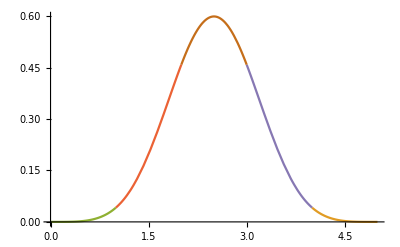

```mathematica
(*IMPORTANT: Before use, save the box spline that you want to color plot in the function "f" and update the plot ranges.*)
toFuncs[i_]:=If[i[[2]],i[[1]],Null]
funcs=Map[toFuncs,PiecewiseExpand[g[x]][[1]]];
Plot[funcs,{x,0,5}]
```

```mathematica
Function for plotting 3D pieces of the box spline as a unique color
```

```mathematica
(*IMPORTANT: Before use, save the box spline that you want to color plot in the function "f" and update the plot ranges.*)
toFuncs[i_]:=If[i[[2]],i[[1]],Null]
funcs=Map[toFuncs,PiecewiseExpand[f[x,y]][[1]]];
Plot3D[funcs,{x,0,3},{y,0,3},Boxed->False,ViewPoint->{1.3, -2.4, 2.}]
```

-Graphics3D-

Figures for Paper

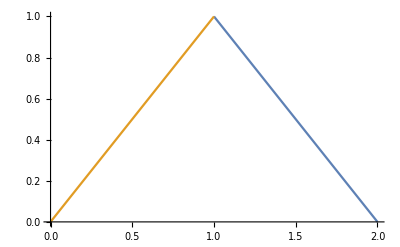

```mathematica
(* Direction vector (1 1) *)
```

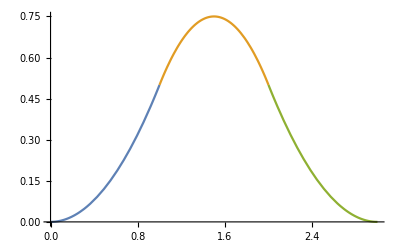

```mathematica
(* Direction vector (1 1 1) *)
```

```mathematica
(* Direction vector ({{1, 0, 1, 0}, {0, 1, 0, 1}}) *)
```

-Graphics3D-

```mathematica
(* Direction vector ({{1}, {0}} {{0}, {1}} {{1}, {0}} {{0, 1, 0}, {1, 0, 1}}) *)
```

-Graphics3D-

Workspace for testing ideas

The pattern for computing a piecwise quadratic continuous box spline in n dimensional space:
     0 ≤ x < 1         1 ≤ x < 2           2 ≤ x < 3
  1/2^n            x^2            -(2 x^2-6x+3)             (x-3)^2

```mathematica
f[x_]=BoxEval[(x),({{1, 1, 1, 1}})]//Simplify
```

Piecewise[{{x^3/6, 0<x≤1}, {2/3-2 x+2 x^2-x^3/2, 1<x≤2}, {-1/6 (-4+x)^3, 3≤x<4}, {-22/3+10 x-4 x^2+x^3/2, 2<x<3}, {0, True}}]

```mathematica
g[x_]:=-22/3+10 x-4 x^2+x^3/2;
h[x_]:=2/3-2 x+2 x^2-x^3/2;
g''[2]
h''[2]
```

-2

-2

```mathematica
f[x_,y_]=BoxEval[({{x}, {y}}),({{1, 0, 1, 0, 1, 0}, {0, 1, 0, 1, 0, 1}})]//Simplify
```

Piecewise[{{1/4 (-3+x)^2 (-3+y)^2, 2≤x<3&&2≤y<3}, {1/4 (-3+x)^2 y^2, 2≤x<3&&0<y≤1}, {(x^2 y^2)/4, 0<x≤1&&0<y≤1}, {-1/4 x^2 (3-6 y+2 y^2), 0<x≤1&&1<y<2}, {-1/4 (3-6 x+2 x^2) y^2, 1<x<2&&0<y≤1}, {-1/4 (3-6 x+2 x^2) (-3+y)^2, 1<x<2&&2≤y<3}, {-1/4 (-3+x)^2 (3-6 y+2 y^2), 2≤x<3&&1<y<2}, {1/4 x^2 (-3+y)^2, 0<x≤1&&2≤y<3}, {1/4 (3-6 x+2 x^2) (3-6 y+2 y^2), 1<x<2&&1<y<2}, {0, True}}]

```mathematica
f[x_,y_,z_]=BoxEval[({{x}, {y}, {z}}),({{1, 0, 0, 1, 0, 0, 1, 0, 0}, {0, 1, 0, 0, 1, 0, 0, 1, 0}, {0, 0, 1, 0, 0, 1, 0, 0, 1}})]//Simplify
```

Piecewise[{{1/8 (-3+x)^2 (-3+y)^2 (-3+z)^2, 2≤x<3&&2≤y<3&&2≤z<3}, {1/8 x^2 (-3+y)^2 (-3+z)^2, 0<x≤1&&2≤y<3&&2≤z<3}, {1/8 (-3+x)^2 y^2 (-3+z)^2, 2≤x<3&&0<y≤1&&2≤z<3}, {1/8 (-3+x)^2 (-3+y)^2 z^2, 2≤x<3&&2≤y<3&&0<z≤1}, {1/8 x^2 (-3+y)^2 z^2, 0<x≤1&&2≤y<3&&0<z≤1}, {1/8 (-3+x)^2 y^2 z^2, 2≤x<3&&0<y≤1&&0<z≤1}, {1/8 x^2 y^2 z^2, 0<x≤1&&0<y≤1&&0<z≤1}, {-1/8 (3-6 x+2 x^2) (3-6 y+2 y^2) (3-6 z+2 z^2), 1<x<2&&1<y<2&&1<z<2}, {-1/8 x^2 y^2 (3-6 z+2 z^2), 0<x≤1&&0<y≤1&&1<z<2}, {-1/8 x^2 (3-6 y+2 y^2) z^2, 0<x≤1&&1<y<2&&0<z≤1}, {-1/8 x^2 (3-6 y+2 y^2) (-3+z)^2, 0<x≤1&&1<y<2&&2≤z<3}, {-1/8 x^2 (-3+y)^2 (3-6 z+2 z^2), 0<x≤1&&2≤y<3&&1<z<2}, {-1/8 (3-6 x+2 x^2) y^2 z^2, 1<x<2&&0<y≤1&&0<z≤1}, {-1/8 (3-6 x+2 x^2) y^2 (-3+z)^2, 1<x<2&&0<y≤1&&2≤z<3}, {-1/8 (3-6 x+2 x^2) (-3+y)^2 z^2, 1<x<2&&2≤y<3&&0<z≤1}, {-1/8 (3-6 x+2 x^2) (-3+y)^2 (-3+z)^2, 1<x<2&&2≤y<3&&2≤z<3}, {-1/8 (-3+x)^2 y^2 (3-6 z+2 z^2), 2≤x<3&&0<y≤1&&1<z<2}, {-1/8 (-3+x)^2 (3-6 y+2 y^2) z^2, 2≤x<3&&1<y<2&&0<z≤1}, {-1/8 (-3+x)^2 (3-6 y+2 y^2) (-3+z)^2, 2≤x<3&&1<y<2&&2≤z<3}, {-1/8 (-3+x)^2 (-3+y)^2 (3-6 z+2 z^2), 2≤x<3&&2≤y<3&&1<z<2}, {1/8 x^2 y^2 (-3+z)^2, 0<x≤1&&0<y≤1&&2≤z<3}, {1/8 x^2 (3-6 y+2 y^2) (3-6 z+2 z^2), 0<x≤1&&1<y<2&&1<z<2}, {1/8 (-3+x)^2 (3-6 y+2 y^2) (3-6 z+2 z^2), 2≤x<3&&1<y<2&&1<z<2}, {1/8 (3-6 x+2 x^2) y^2 (3-6 z+2 z^2), 1<x<2&&0<y≤1&&1<z<2}, {1/8 (3-6 x+2 x^2) (-3+y)^2 (3-6 z+2 z^2), 1<x<2&&2≤y<3&&1<z<2}, {1/8 (3-6 x+2 x^2) (3-6 y+2 y^2) z^2, 1<x<2&&1<y<2&&0<z≤1}, {1/8 (3-6 x+2 x^2) (3-6 y+2 y^2) (-3+z)^2, 1<x<2&&1<y<2&&2≤z<3}, {0, True}}]